```mathematica
D[(1-x^(1-s))Zeta[s],x]
```

-(1-s) x^-s Zeta[s]

```mathematica
D[x^(1-s)/j^s,x]
```

j^-s (1-s) x^-s

```mathematica
D[x^(1-s)/(j+n/x)^s,x]
```

n s (j+n/x)^(-1-s) x^(-1-s)+(1-s) (j+n/x)^-s x^-s

```mathematica
Expand[(j+n/x)^(-1-s) x^(-1-s)]
```

(j+n/x)^(-1-s) x^(-1-s)

```mathematica
FullSimplify@D[x^(1-s)/(j+n/x)^s,{x,2}]/.x->1
```

j (j+n)^(-2-s) (-2 n+j (-1+s)) s

```mathematica
Expand[j (-2 n+j (-1+s)) s]
```

-j^2 s-2 j n s+j^2 s^2

```mathematica
tes2[n_,s_]:=   (s-1)n^s Zeta[s,n+1]
```

```mathematica
FullSimplify[(-1 -1)(n^-1 Zeta[-1]-Sum[ (n/j)^-1,{j,1,n}])]
```

1+1/(6 n)+n

```mathematica
FullSimplify[(-2 -1)(n^-2 Zeta[-2]-Sum[ (n/j)^-2,{j,1,n}])]
```

3/2+1/(2 n)+n

```mathematica
FullSimplify[(-3 -1)(n^-3 Zeta[-3]-Sum[ (n/j)^-3,{j,1,n}])]
```

2-1/(30 n^3)+1/n+n

```mathematica
FullSimplify[(-4 -1)(n^-4Zeta[-4]-Sum[ (n/j)^-4,{j,1,n}])]
```

5/2-1/(6 n^3)+5/(3 n)+n

```mathematica
FullSimplify[(-5 -1)(n^-5Zeta[-5]-Sum[ (n/j)^-5,{j,1,n}])]
```

3+1/(42 n^5)-1/(2 n^3)+5/(2 n)+n

```mathematica
Expand[(-6 -1)(n^-6Zeta[-6]-Sum[ (n/j)^-6,{j,1,n}])]
```

7/2+1/(6 n^5)-7/(6 n^3)+7/(2 n)+n

```mathematica
Expand[(-7 -1)(n^-7Zeta[-7]-Sum[ (n/j)^-7,{j,1,n}])]
```

4-1/(30 n^7)+2/(3 n^5)-7/(3 n^3)+14/(3 n)+n

```mathematica
Expand[(-8 -1)(n^-8Zeta[-8]-Sum[ (n/j)^-8,{j,1,n}])]
```

9/2-3/(10 n^7)+2/n^5-21/(5 n^3)+6/n+n

```mathematica
Expand[(-9 -1)(n^-9Zeta[-9]-Sum[ (n/j)^-9,{j,1,n}])]
```

5+5/(66 n^9)-3/(2 n^7)+5/n^5-7/n^3+15/(2 n)+n

```mathematica
Expand[(-9 -1)(n^-9Zeta[-9]-Sum[ (n/j)^-9,{j,1,n}])]
```

5+5/(66 n^9)-3/(2 n^7)+5/n^5-7/n^3+15/(2 n)+n

```mathematica
FullSimplify[(2 -1)(n^2 Zeta[2]-Sum[ (n/j)^2,{j,1,n}])]
```

n^2 PolyGamma[1,1+n]

```mathematica
FullSimplify[(3 -1)(n^3 Zeta[3]-Sum[ (n/j)^3,{j,1,n}])]
```

-n^3 PolyGamma[2,1+n]

```mathematica
FullSimplify[(4 -1)(n^4 Zeta[4]-Sum[ (n/j)^4,{j,1,n}])]
```

3 n^4 HurwitzZeta[4,1+n]

```mathematica
FullSimplify[(5 -1)(n^5 Zeta[5]-Sum[ (n/j)^5,{j,1,n}])]
```

-1/6 n^5 PolyGamma[4,1+n]

```mathematica
FullSimplify[(6 -1)(n^6 Zeta[6]-Sum[ (n/j)^6,{j,1,n}])]
```

5 n^6 HurwitzZeta[6,1+n]

```mathematica
FullSimplify[(7 -1)(n^7 Zeta[7]-Sum[ (n/j)^7,{j,1,n}])]
```

6 n^7 HurwitzZeta[7,1+n]

```mathematica
Expand[FullSimplify[((-5 -1)(n^-5Zeta[-5]-Sum[ (n/j)^-5,{j,1,n}])+(-5-1)/2)]/n]
```

1+1/(42 n^6)-1/(2 n^4)+5/(2 n^2)

```mathematica
Expand[((-5 -1)n^-(6) (Zeta[-5]- Sum[ (1/j)^-5,{j,1,n}]))]
```

1+1/(42 n^6)-1/(2 n^4)+5/(2 n^2)+3/n

```mathematica
Limit[ 1+1/(42 n^6)-1/(2 n^4)+5/(2 n^2)+3/n,n->Infinity]
```

1

```mathematica
ta[n_,s_]:=((s -1)n^(s-1) (Zeta[s]- Sum[ (1/j)^s,{j,1,n}]))
ta2[n_,s_]:=((s -1)n^(s-1) (- Sum[ (1/j)^s,{j,1,n}]))
ta3[n_,s_]:= Sum[j^-s,{j,1,n}] - n^(-s)/(s-1)
```

```mathematica
N@ta2[10000,-3+I]
```

1.0002-0.0000500058 ⅈ

```mathematica
ta3[1000000,-.5]
```

6.66668×10^8

```mathematica
Zeta[.5]
```

-1.46035

```mathematica
tes5[n_,s_]:=Zeta[s]
tso[n_,s_]:=1/ (s-1)/n^(s-1)+Sum[ (1/j)^s,{j,1,n}]
tso2[n_,s_]:=Sum[ (1/j)^s,{j,1,n}]-n^(1-s)/ (1-s)
tso2a[n_,s_]:={Sum[ (1/j)^s,{j,1,n}],n^(1-s)/ (1-s)}
tso2b[n_,s_]:=Sum[ 1/j^s-1/(n^s(1-s)),{j,1,n}]
tso3[n_,s_]:=HarmonicNumber[n,s]-n^(1-s)/ (1-s)
tso4[n_,s_]:=n^(1-s)/ (s-1)+(Zeta[s]-Zeta[s,n])
tso5[n_,s_]:=Sum[ 1/j^s,{j,1,n}]-2^(1-s)Sum[ 1/j^s,{j,1,n/2}]
tso5a[n_,s_]:=(HarmonicNumber[n,s]-2^(1-s)HarmonicNumber[n/2,s])/(1-2^(1-s))
```

```mathematica
tes5[1000000,.5+I]
```

0.143936-0.7221 ⅈ

```mathematica
N@tso2[1000000000000,.2]
```

-0.731937

```mathematica
N@tso2b[1000000000000,.2]
```

-0.73193

```mathematica
Zeta[.2]
```

-0.733921

```mathematica
N@tso2a[1000000000000,N[ZetaZero[1]]-.1]
```

{967156.+565340. ⅈ,967156.+565340. ⅈ}

```mathematica
ag[n_,s_]:=-2^(1-s)Sum[ j^-s,{j,1,n/2}]
ag2[n_,s_]:=-n^(1-s)/ (1-s)
```

```mathematica
ag[100000000,.5+I]
```

-310.456-8937.95 ⅈ

```mathematica
ag2[100000000,.5+I]
```

-310.951-8938.87 ⅈ

```mathematica
N@Zeta[1+1/2+11I]
```

1.18046-0.274549 ⅈ

```mathematica
N[tso3[100000000000,ZetaZero[1]]]
```

1.5673×10^-6+2.0663×10^-7 ⅈ

```mathematica
N[tso5a[10000000000000,ZetaZero[1]]]
```

2.28745×10^-8+6.42544×10^-8 ⅈ

```mathematica
p1[n_,s_]:=HarmonicNumber[n,s]
p1i[n_,s_]:=p1[n,1-s]
p2[n_,s_]:=n^(1-s)/ (1-s)
p2i[n_,s_]:=p2[n,1-s]
p12[n_,s_]:=HarmonicNumber[n,s]-n^(1-s)/ (1-s)
p12i[n_,s_]:=p12[n,s]-p12[n,1-s]
p12j[n_,s_]:=p12[n,s]+p12[n,1-s]
p12k[n_,s_]:=p12[n,s]p12[n,1-s]
```

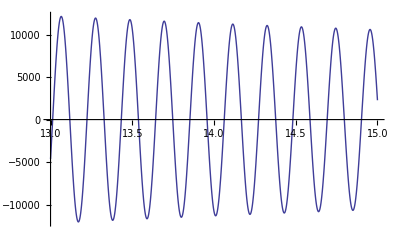

```mathematica
Plot[Re[ p2i[10000000000000,.4+t I]],{t,13,15}]
```

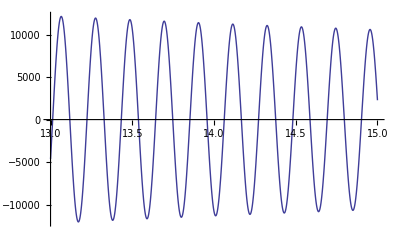

```mathematica
Plot[Re[ p1i[10000000000000,.4+t I]],{t,13,15}]
```

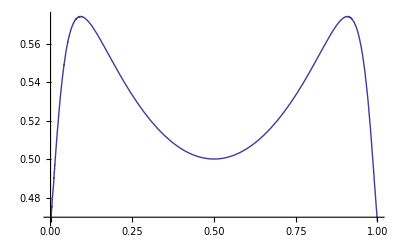

```mathematica
Plot[Abs[ p12k[10000000000000,t+13.14I]],{t,0,1}]
```

```mathematica
tso2b[n_,s_]:=Sum[ 1/j^s-1/(n^s(1-s)),{j,1,n}]
```

```mathematica
tso2b[10000000000,.5]
```

-1.46035

```mathematica
tso2c[10000000000,.5]
```

2.×10^10

```mathematica
tc[n_,s_]:= (s-1)( Zeta[s]-Sum[ j^-s, {j,1,n}])-n^(1-s)
```

```mathematica
Chop@tc[10000000000,.75+I]
```

1.15745×10^-8+1.14738×10^-8 ⅈ